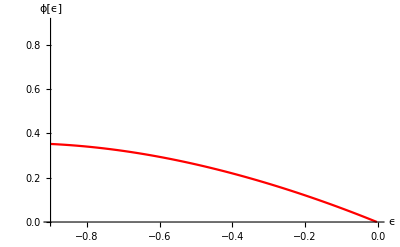

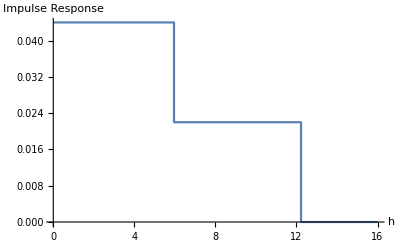

-Graphics-

/Users/aroberts/Publications/2018_Morphology/Figures/Figure13

```mathematica
ClearAll["Global`*"]

(* 
   ridgepack_JAMES_figure13 - Generates Figure 13 in JAMES Variation Ridging paper 

 This script generates Figure 13 from:   

Roberts, A.F., E.C. Hunke, S.M. Kamal, W.H. Lipscomb, C. Horvat, W. Maslowski (2019),
   Variational Method for Sea Ice Ridging in Earth System Models, J. Adv. Model Earth Sy.

 Contact: Andrew Roberts, afroberts@lanl.gov

  Author: Andrew Roberts, Naval Postgraduate School, April 2018
  Updated: Andrew Roberts, Los Alamos National Laboratory, December 2018

*)

(***** Global Settings ********************************************************)

(* Working directory *)
SetDirectory[NotebookDirectory[]]; 

(* Parameter Space *)
ρ:=917; (* Density of sea ice *)
ρw:=1026; (* Density of sea water *)
g:=9.8; (* Acceleration due to gravity *)
hF:=2; (* Initial thickness of sea ice *)
ϕi:=0; (* Initial porosity of sea ice *)

(* Strains to be plotted *)
ϵx:={-0.20,-0.40,-0.60};

(* set density delta *)
Δρ:=(ρw-ρ);


(***** Solve for Porosity *****************************************************)

(* Solve for αR as listed in Appendix C *)
λ[ϵ_,ϕ_]:=(ϕ+ϕ ϵ-ϵ);
α[ϵ_,ϕ_]:=2ArcTan[√(((5(λ[ϵ,ϕ])^2+6λ[ϵ,ϕ]+3)-√((5 λ[ϵ,ϕ]^2+6λ[ϵ,ϕ]+3)^2-4 (λ[ϵ,ϕ])^4))/(2 (λ[ϵ,ϕ])^2))];

(* Solve for shape of individual ridge *)
hFf:=Δρ/ρw  hF;
hFd:=ρ/ρw hF;
hR[ϵ_]:=hF/(1+ϵ);
hRf[ϵ_]:=Δρ/ρw  hR[ϵ];
hRd[ϵ_]:=ρ/ρw hR[ϵ];
HK[ϵ_,ϕ_]:=(2 hRd[ϵ])/(1-ϕ)-hFd;
HS[ϵ_,ϕ_]:=hFf+2 √((hRd[ϵ]/(1-ϕ)-hFd)(hRf[ϵ]/(1-ϕ)-hFf));
LK[ϵ_,ϕ_]:=2(HK[ϵ,ϕ]-hFd)Cot[α[ϵ,ϕ]];
LS[ϵ_,ϕ_]:=2(HS[ϵ,ϕ]-hFf)Cot[α[ϵ,ϕ]];


(* Potential Energy *)
VR[ϵ_,ϕ_]:= Δρ g  (1-ϕ)(1/2 hFd LK[ϵ,ϕ] +1/8 LK[ϵ,ϕ]^2 Tan[α[ϵ,ϕ]]) +  ρ g  (1-ϕ)(1/2 hFf LK[ϵ,ϕ] +1/8 LS[ϵ,ϕ]^2 Tan[α[ϵ,ϕ]]) ;

(* Calculate Dilation Field *)
dVRdϵ[ϵ_,ϕ_] = D[VR[ϵ,ϕ],ϵ];
dVRdϕ[ϵ_,ϕ_] = D[VR[ϵ,ϕ],ϕ];

(* Calculate gradient of streamfunction *)
dϕdϵ[ϵ_,ϕ_]=dVRdϕ[ϵ,ϕ]/dVRdϵ[ϵ,ϕ];

(* Numerical Solution of Steamline Passing through Origin using Residual Method *) 
cont={ϕ'[ϵ]==dϕdϵ[ϵ,ϕ[ϵ]], ϕ[-0.001]==0};
solu=NDSolve[cont,ϕ[ϵ],{ϵ,-0.98,-0.001},Method->{"EquationSimplification"->"Residual"}];

(* Calculate porosity based on strain *)
ϕR[ϵR_]=Part[((ϕ[ϵ]/.solu)/.ϵ-> ϵR),1];

(* Provide supplemental angle of repose for convenience *)
αR[ϵR_]=α[ϵR,ϕR[ϵR]];

(***** Define impulse responsee function **************************************)

(* Strain Operator *)
Γ[ϵR_]=1/2((1+ϵR)(1-ϕR[ϵR]))/(ϕR[ϵR]+ϵR  ϕR[ϵR] -ϵR);

(* First Step location *)
Λ1[hi_,h_,ϵR_]=((ρw Γ[ϵR])/(ρ -√(Δρ ρ))h/hi);

(* Second Step location *)
Λ2[hi_,h_,ϵR_]=((ρw Γ[ϵR])/(ρ +√(Δρ ρ))h/hi);

(* Magnitude ("height") of steps *)
ν[hi_,ϕ_,ϵR_]=1/2 ρw/ρ 1/hi(1+ϵR) DiracDelta[ϕ-ϕR[ϵR]] Γ[ϵR];

(* Define Impulse Response Function *)
(*fh[ϵR_,hi_,h_,ϕ_]= ν[hi,ϕ,ϵR](2HeavisidePi[Λ1[hi,h,ϵR]-0.5] +(HeavisidePi[Λ2[hi,h,ϵR]-0.5]-HeavisidePi[Λ1[hi,h,ϵR]-0.5]));*)

fh[ϵR_,hi_,h_,ϕ_]= ν[hi,ϕ,ϵR](HeavisidePi[Λ1[hi,h,ϵR]-0.5] +HeavisidePi[Λ2[hi,h,ϵR]-0.5]);

(*fh[ϵR_,hi_,h_,ϕ_]= ν[hi,ϕ,ϵR](HeavisideTheta[Λ1[hi,h,ϵR]] -HeavisideTheta[Λ1[hi,h,ϵR]-1] +HeavisideTheta[Λ2[hi,h,ϵR]]-HeavisideTheta[Λ2[hi,h,ϵR]-1]);*)

(***** Define Thickness Distribution ******************************************)

(* Initial thickness distribution *)
gi[h_,ϕ_]=DiracDelta[h-hF,ϕ-ϕi];

(* Final thickness distributions *)
gf[ϵR_,h_,ϕ_]=Convolve[gi[hri,ϕri],fh[ϵR,h-hri,hri,ϕri],{hri,ϕri},{h,ϕ}];


(***** Plot Distributions ****************************************************)

(* Plot Characteristics *)
resolution=20000; (* Resolution of Dirac Delta approximation *)
points=1000; (* Plotpoints *)
hmax=16; (* Maximum thickness *)
ϕmax=0.3; (* Maximum porosity *)
gmax=0.55; (* Maximum g *)
prange={{0,hmax},{0,ϕmax},{0,gmax}}; (* Range of plot *)
legpos={0.8,0.6}; (* Legend position *)

(* Plot ϕ[ϵ] function to check values *)
Plot[{ϕ[ϵ]/.solu[[1]]}, {ϵ,-0.9,-0.001}, PlotRange-> {{-0.9,-0.001},{0.001,0.9}},PlotStyle->Red,AxesLabel->{"ϵ","ϕ[ϵ]"}]

(* Plot impulse response function to check values*)
fhplot[h_]:=Evaluate[fh[ϵx[[3]],hF,h,ϕR[ϵx[[3]]]]/.DiracDelta[a_]:>  UnitStep[1/resolution-(a^2)]]
Plot[fhplot[h],{h,0,hmax},Exclusions-> None,PlotPoints->points,AxesLabel->{"h","Impulse Response"}]

(* Plot initial Diract Delta function *)
giplot2d[h_,ϕ_]:= Evaluate[0.99gmax  gi[h,ϕ]/.DiracDelta[a_,b_]:>  UnitStep[1/resolution-(a^2+b^2)]]
A1=ParametricPlot3D[{h,ϕi,giplot2d[h,ϕi]},{h,0,hmax},Exclusions-> None,PlotPoints->points,PlotStyle->{RGBColor[0.5,0,1]},PlotRange->prange,PlotLegends->Placed[{"ϵ_R=0"},legpos], LabelStyle->{FontFamily->"Times",FontSize->18}];

(* Superimpose arrow to annotate Diract Delta *)
A2=Graphics3D[{RGBColor[0.5,0,1],Arrowheads[0.003 gmax],Arrow[{{hF,0,0},{hF,0,gmax}}]}];

A1α =Graphics3D[{Text[Rotate[Style["α_R=0°",RGBColor[0.5,0,1]],-0.48],{0.8+hF,0.01,0}]}];

(* Plot evolution of thickness distribution *)
gfplot2d[h_,ϵR_]:=Evaluate[gf[ϵR,h,ϕR[ϵR]]/.DiracDelta[a_]:>  UnitStep[1/resolution-(a^2)]]

B1=ParametricPlot3D[{h,ϕR[ϵx[[1]]],gfplot2d[h,ϵx[[1]]]},{h,0,hmax},Exclusions-> None, PlotPoints->points,PlotStyle->{RGBColor[0.5,0,0.5]},PlotRange->prange,PlotLegends->Placed[{"ϵ_R="<>TextString[ϵx[[1]]]},legpos],LabelStyle->{FontFamily->"Times",FontSize->18}];

B1α =Graphics3D[{Text[Rotate[Style["α_R="<>TextString[Round[180 αR[ϵx[[1]]]/Pi,2]]<>"°",RGBColor[0.5,0,0.5]],-0.45],{0.8+5,ϕR[ϵx[[1]]]+0.01,0}]}];

B2=ParametricPlot3D[{h,ϕR[ϵx[[2]]],gfplot2d[h,ϵx[[2]]]},{h,0,hmax},Exclusions-> None, PlotPoints->points,PlotStyle->{RGBColor[0.75,0.25,0.25]},PlotRange->prange,PlotLegends->Placed[{"ϵ_R="<>TextString[ϵx[[2]]]},legpos],LabelStyle->{FontFamily->"Times",FontSize->18}];

B2α =Graphics3D[{Text[Rotate[Style["α_R="<>TextString[Round[180 αR[ϵx[[2]]]/Pi,2]]<>"°",RGBColor[0.75,0.25,0.25]],-0.42],{0.8+8,ϕR[ϵx[[2]]]+0.01,0}]}];

B3=ParametricPlot3D[{h,ϕR[ϵx[[3]]],gfplot2d[h,ϵx[[3]]]},{h,0,hmax},Exclusions-> None, PlotPoints->points,PlotStyle->{RGBColor[1,0.25,0]},PlotRange->prange,PlotLegends->Placed[{"ϵ_R="<>TextString[ϵx[[3]]]},legpos],LabelStyle->{FontFamily->"Times",FontSize->18}];

B3α =Graphics3D[{Text[Rotate[Style["α_R="<>TextString[Round[180 αR[ϵx[[3]]]/Pi,2]]<>"°",RGBColor[1,0.25,0]],-0.40],{0.8+10.5,ϕR[ϵx[[3]]]+0.028,0}]}];

(* Combine plot *)
h1=Show[A1,A2, A1α, B1,B1α,B2, B2α,B3, B3α,AxesLabel->{Rotate[Row[{Style["h",FontSlant->Italic]," (m)"}],-0.5],Rotate["ϕ_R",Pi/2-0.55], Rotate[Row[{Style["a_R(h, ",FontSlant->Italic],"ϕ_R)"}],1.7]},BoxRatios->{1,1,1},Axes->True,Boxed->True,ViewPoint->{2.277,-2.747,1.897},Ticks->{Range[2,hmax,2],Range[0,ϕmax,0.05],Range[0,gmax,0.1]},BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->Full]

(* Print to EPS and PDF in current directory*)
Directory[]
Export["ridgepack_JAMES_figure13.eps",h1,"EPS"];
Export["ridgepack_JAMES_figure13.pdf",h1,"PDF"];
```